```mathematica
data={{518.672, 0.775}, {548.996, 0.888}, {687.858, 1.504}, {740.858, 1.712}, {820.264, 2.029}};
tol={0.001, 0.001, 0.001, 0.001, 0.01};
```

```mathematica
sim=  Flatten[MapThread[Function[{a},{#1[[1]],a}]/@RandomVariate[NormalDistribution[#1[[2]],#2],200]&,{data,tol}],1];
fit=LinearModelFit[sim,x,x]
```

FittedModel[-1.40841+0.00420607 x]

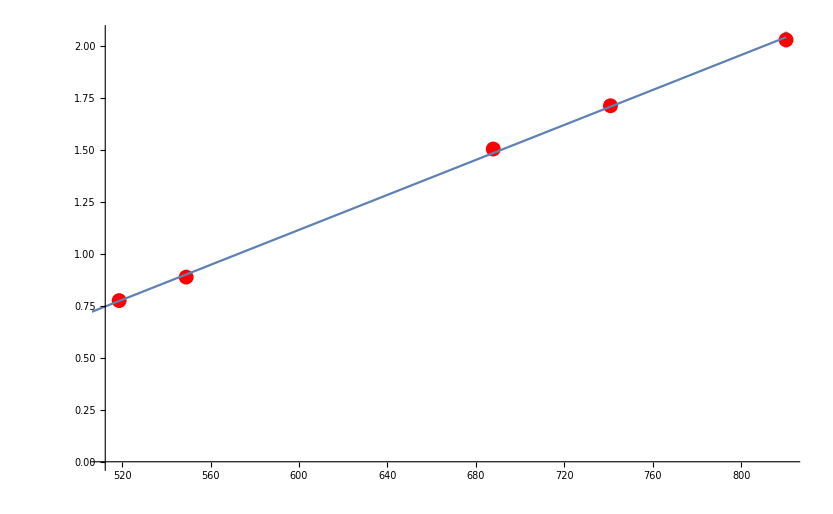

```mathematica
Show[{
ListPlot[sim,PlotStyle->{Opacity[.25],Gray}],
ListPlot[data,PlotStyle->Red],
Plot[{fit[x]},{x,0,data[[-1,1]]},Frame->True,FrameLabel->{x,y},LabelStyle->Directive[Red,Bold]]
}]
```